```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCAnalysis3`
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/SED/GDC_CHP_AR_SED_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/SED/GDC_CHP_BR_SED_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.,0.,0.,0.}

{-1,-1,-1,-1,-1}

{-1,-1,-1,-1,-1}

```mathematica
tsAR={3,4,5,6,7,8};
tsBR={3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "SED", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "SED", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "SED", "F"]
```

{{3,0.010101},{3.5,0.010101},{4,0.010101},{4.5,0.00819672},{5,0.00819672},{5.5,0.00595238},{6,0.00595238},{6.5,0.00595238},{7,0.00348432},{7.5,0.00348432},{8,1.}}

{{3,0.00966208},{3.5,0.00964112},{4,0.00964112},{4.5,0.00793085},{5,0.00793085},{5.5,0.00584619},{6,0.00584619},{6.5,0.00584746},{7,0.00343173},{7.5,0.00343216},{8,1.}}

{{3,0.916712},{3.5,0.912907},{4,0.912907},{4.5,0.937164},{5,0.937164},{5.5,0.964946},{6,0.964946},{6.5,0.965358},{7,0.970264},{7.5,0.970501},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/SED/SED_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/SED/SED_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/SED/SED_F.txt"]
```

{{3,0.00505051},{3.5,0.00505051},{4,0.00505051},{4.5,0.00409836},{5,0.00409836},{5.5,0.00297619},{6,0.00297619},{6.5,0.00297619},{7,0.00348432},{7.5,0.00348432},{8,1.}}

{{3,0.00480165},{3.5,0.00481119},{4,0.00481119},{4.5,0.00396334},{5,0.00396334},{5.5,0.00292235},{6,0.00292235},{6.5,0.00292298},{7,0.00343114},{7.5,0.00343155},{8,1.}}

{{3,0.906082},{3.5,0.909517},{4,0.909517},{4.5,0.936213},{5,0.936213},{5.5,0.964462},{6,0.964462},{6.5,0.964873},{7,0.969934},{7.5,0.970163},{8,1}}

```mathematica
(*dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "SED"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=SED geg EV&BK=SED",PlotMarkers->{{"X",12}, {"S",12}},ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "SED"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_SED geg EV&BK=SED",PlotMarkers->{{"X",12}, {"S",12}},ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "SED"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_SED geg EV&BK=SED",PlotMarkers->{{"X",12}, {"S",12}},ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]*)
```

```mathematica
(* dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]
Map[compCHMaxFunc[First[persMixFunc["SED"]], #, tatCH , dojBR]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["SED"]],# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["SED"]],# , dojBR,  "CH", "PEN"]&,{4.5}]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["SED"]];
pers="SED";
```

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,tsAR]
```

{{3,0.666667},{4,0.8},{5,0.8},{6,0.666667},{7,0.666667},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR,pers];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,pers];
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR,pers];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV];
fVVHist=vvHistPointsFunc[fVV];
```

11

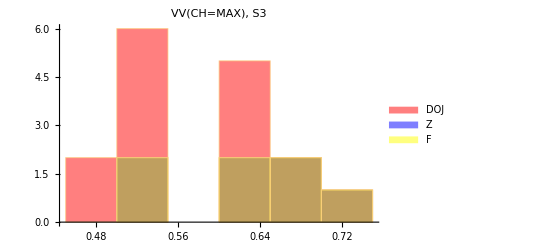
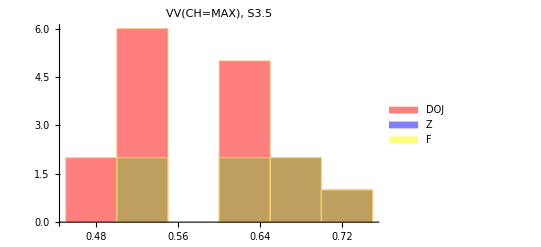
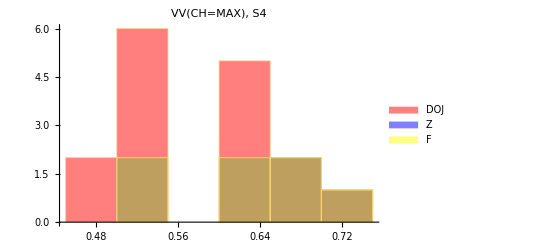
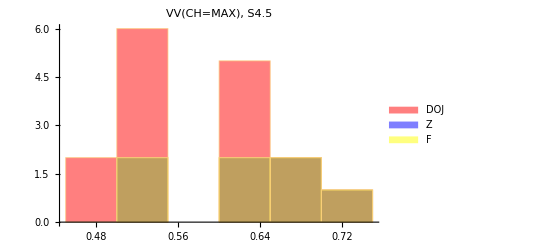
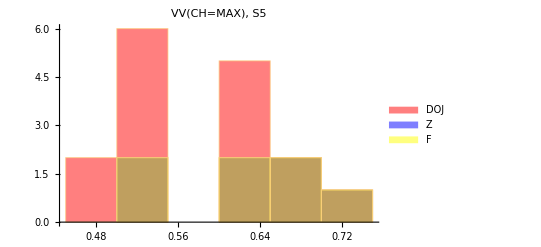
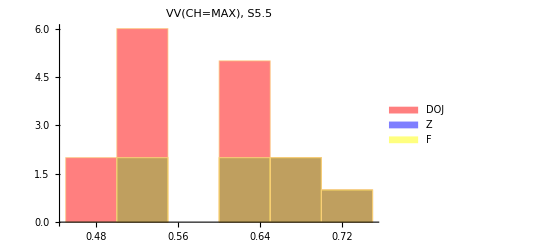
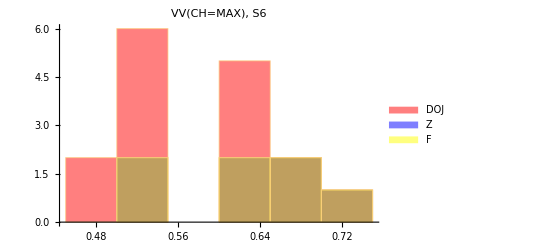
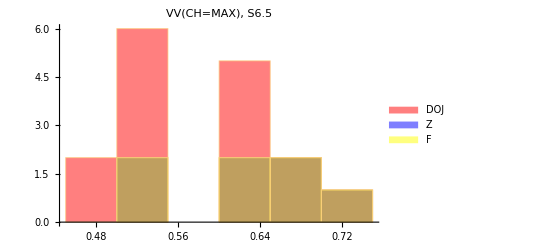
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=SED",PlotMarkers->{{"D",12}}, PlotRange->All]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=SED",PlotMarkers->{{"Z",12}}, PlotRange->All]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=SED",PlotMarkers->{{"F",12}}, PlotRange->All]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=SED",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;11]]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/SED/"];
(*Export["COMP_DOJ_CHTAT_CHMAX_SED.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_SED.jpeg",confMAX,ImageResolution->300]*)
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_SED.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_SED.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_SED.txt"]
Export["VV_CHMAX_HIST_SED.jpeg",histOut,ImageResolution->300]
```

VV_CHMAX_HIST_SED.jpeg